```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/500nm.dat"]
```

{{1.46129,0.137934},{1.36603,0.199424},{1.32759,0.204328},{1.2815,0.216965},{1.23231,0.22594},{1.21009,0.244435},{1.18279,0.225062},{1.15809,0.186314},{1.13892,0.148161},{1.12738,0.137499},{1.09219,0.183155},{1.09146,0.235862},{1.09503,0.286982},{1.10053,0.298696},{1.1079,0.296989},{1.12128,0.300475},{1.13179,0.262057},{1.14273,0.284352},{1.16583,0.276267},{1.1846,0.272771},{1.20387,0.301141},{1.22314,0.26934},{1.24682,0.263902}}

0.494314-0.21579 x

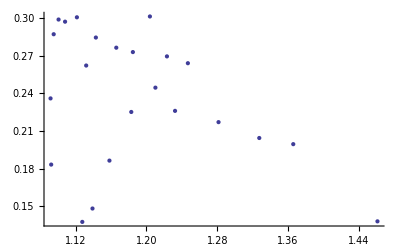

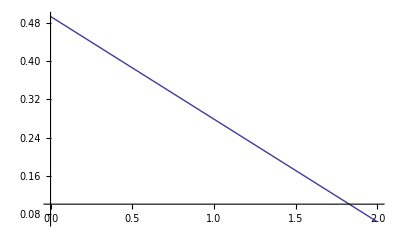

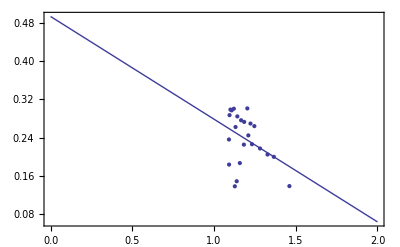

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```